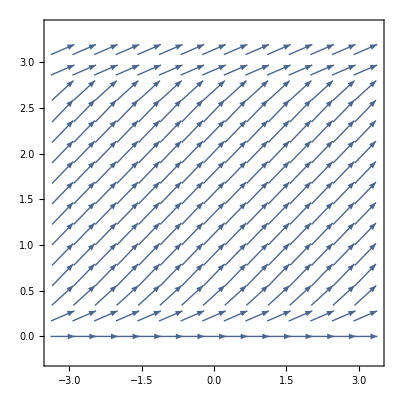

```mathematica
f[x_, y_, theta_] :=Piecewise[{{{Cos[y], Sin[y]}, y<theta},
{{Cos[theta], Sin[theta]},theta<y<Pi-theta},
{{Cos[Pi-y], Sin[Pi-y]}, Pi-theta<y<Pi}}  ]
VectorPlot[f[x, y, .5],{x, -Pi, Pi}, {y, 0, Pi} ]
```

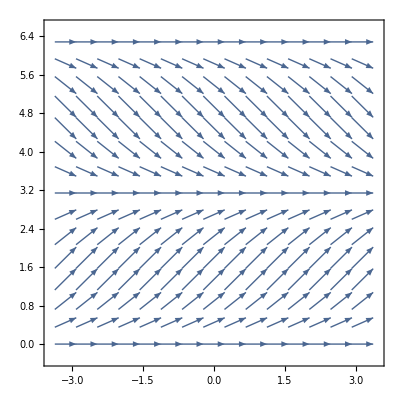

```mathematica
VectorPlot[{1, Sin[y]},{x, -Pi, Pi}, {y, 0, 2Pi} ]
```